# Yield and Estimated time for Polarization Measurement

## by p (p, p) p elastic scattering

the differential cross section is 
	dσ/dΩ=(dσ/dΩ)_0(1+A_y n̂·P⃗)
where A_y is analysing power and P_y is polarization of the target.

the yield is dependence on
N_B number of particle per sec of the beam
f   fraction of the beam on the target
N_T number of particle per unit area of the target
ϵ the detector efficiency
α the DAQ life time
Ω acceptance of the detector 

Y=T N_B N_T ϵ α Ω dσ/dΩ=∫N_B N_T ϵ α  dσ/dΩ ΔΩ

due to the polarization on anaylsing power, the left yield and right yield are difference

Y_L=T N_B N_T ϵ α ∫(dσ/dΩ)_0(1+A_y(θ)P_y)ΔΩ
Y_R=T N_B N_T ϵ α ∫(dσ/dΩ)_0(1-A_y(θ)P_y)ΔΩ
A_y(θ)P_y= (Y_L-Y_R)/(Y_L+Y_R)

the error propagation:

ΔP_y=√(((∂P_y)/(∂Y_L))^2(ΔY_L)^2+((∂P_y)/(∂Y_R))^2(ΔY_R)^2)
=2/A_y √((Y_L Y_R)/(Y_L+Y_R)^3)

for small asymetry, the Y_L~Y_R~Y/2

ΔP_y~  1/(A_y √Y)

```mathematica
a= 1;
Remove[a]
```

## Calculaion

### Data of Xsec and Ay

```mathematica
Dsc200Dist=Interpolation[
{{20.00,15.30},{25.00,14.65},
{30.00,13.80},{35.00,12.78},
{40.00,11.69},{45.00,10.59},
{50.00,9.495},{55.00,8.377},
{60.00,7.205},{65.00,5.986},
{70.00,4.753}}];
Dsc260Dist=Interpolation[
{{5.00,16.62},{10.00,16.16},
{15.00,15.98},{20.00,15.57},
{25.00,14.93},{30.00 ,14.01},
{35.00 ,12.88},{40.00 ,11.70},
{45.00 ,10.55},{50.00 ,9.431},
{55.00 ,8.302},{60.00 ,7.112},
{65.00 ,5.865},{70.00 ,4.616},
{75.00,3.401},{80.00,2.218},
{85.00,1.22},{90.00,0}}];
Dsc260CM[x_]:=3.8
Dsc300Dist=Interpolation[
{{10.00,16.86},{15.00,16.55},
{20.00,16.05},{25.00,15.28},
{30.00 ,14.19},{35.00 ,12.93},
{40.00 ,11.67},{45.00 ,10.48},
{50.00 ,9.373},{55.00 ,8.268},
{60.00 ,7.105},{65.00 ,5.873},
{70.00 ,4.625}}];
```

```mathematica
Ay200Dist=Interpolation[
{{20.000,0.3049},{25.000,0.2735},
{30.000,0.2159},{35.000,0.1426},
{40.000,0.06048},{45.000,-0.02470},
{50.000,-0.1076},{55.000,-0.1833},
{60.000,-0.2466},{65.000,-0.2909},
{70.000,-0.3074}}];
Ay260Dist=Interpolation[
{{10.000,0.3169},{15.000,0.3751},
{20.000,0.3723},{25.000,0.3233},
{30.000,0.2479},{35.000,0.1586},
{40.000,0.06205},{45.000,-0.03654},
{50.000,-0.1323},{55.000,-0.2207},
{60.000,-0.2971},{65.000,-0.3545},
{70.000,-0.3805}}];
Ay260CMDist=Interpolation[
{{00,0},{05,0.01899},
{10,0.1779},{15,0.2544},
{20,0.3055},{25,0.3442},
{30,0.3693},{35,0.3802},
{40,0.3778},{45,0.3638},
{50,0.3404},{55,0.3097},
{60,0.2737},{65,0.2337},
{70,0.1906},{75,0.1450},
{80,0.09769},{85,0.04914},
{90,0},{95,-0.04913},
{100,-0.09768},{105,-0.1450},
{110,-0.1906},{115,-0.2337},
{120,-0.2737},{125,-0.3097},
{130,-0.3404},{135,-0.3638},
{140,-0.3778},{145,-0.3802},
{150,-0.3693},{155,-0.3443},
{160,-0.3055},{165,-0.2545},
{170,-0.1779},{175,-0.0190},
{180,0}}];
Ay300Dist=Interpolation[
{{0,0},{5,0.2122},
{10,0.3528},{15,0.4140},
{20.000,0.4042},{25.000 ,0.3453},
{30.000 ,0.2611},{35.000 ,0.1641},
{40.000 ,0.06056},{45.000,-0.04442},
{50.000,-0.1461},{55.000,-0.2403},
{60.000,-0.3226},{65.000,-0.3861},
{70.000,-0.4171}}];
```

### Display

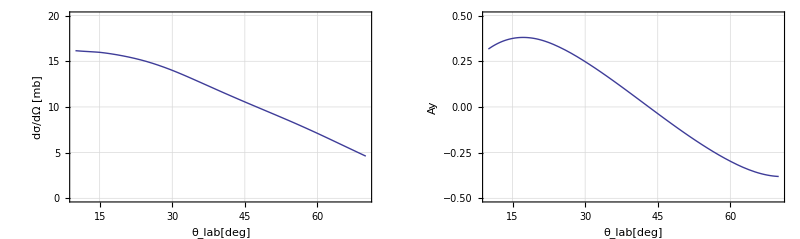

```mathematica
Dsc=Dsc260Dist;
Ay=Ay260Dist;
GraphicsGrid[{{
Plot[{Dsc[x]},{x,10,70},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Frame->True,FrameLabel->{Style["θ_lab[deg]",12],Style["dσ/dΩ [mb]",12]},PlotRange->{0,20}],
Plot[{Ay[x]},{x,10,70},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Frame->True,FrameLabel->{Style["θ_lab[deg]",12],Style["Ay ",12]},PlotRange->{-0.5,0.5}]
}},ImageSize->800]
```

### Acceptance of MWDC

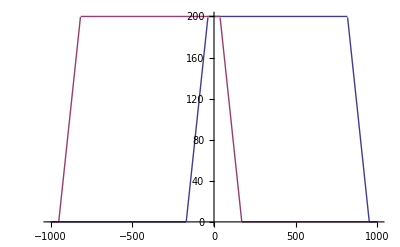

```mathematica
(* first in Lab frame *)
y[x_]:=Piecewise[{{3/2(x+170),200 2/3-170>x>-170},{200,200 (-2/3)+950>x>200 2/3-170},{-3/2(x-950),950>x>200 (-2/3)+950}},0]
Plot[{y[x],y[-x]},{x,-1000,1000}]
```

```mathematica
(* the x component *)
Rot1=RotationMatrix[-60 °,{0,1,0}];
Rot2=RotationMatrix[60 °,{0,1,0}];
X[θ_]:=(2 1022.37)/(√3 Sin[θ π/180]+Cos[θ π/180])Sin[θ π/180]//N
Z[θ_]:=(2 1022.37)/(√3 Sin[θ π/180]+Cos[θ π/180])Cos[θ π/180]//N
Y[θ_]:=y[-(Rot1.{X[θ],0,Z[θ]})[[1]]]
```

```mathematica
Show[
ParametricPlot3D[{
{X[θ],Y[θ],Z[θ]},
{X[θ],-Y[θ],Z[θ]},
{-X[θ],Y[θ],Z[θ]},
{-X[θ],-Y[θ],Z[θ]},
Normalize[{X[θ],Y[θ],Z[θ]}]1000,
Normalize[{X[θ],-Y[θ],Z[θ]}]1000,
Normalize[{-X[θ],Y[θ],Z[θ]}]1000,
Normalize[{-X[θ],-Y[θ],Z[θ]}]1000,
1000{Cos[1/2 ϕela[θ]]Sin[θ °],Sin[1/2 ϕela[θ]]Sin[θ °],Cos[θ °]},
1000{Cos[1/2 ϕela[θ]]Sin[θ °],-Sin[1/2 ϕela[θ]]Sin[θ °],Cos[θ °]},
1000{-Cos[1/2 ϕela[θ]]Sin[θ °],Sin[1/2 ϕela[θ]]Sin[θ °],Cos[θ °]},
1000{-Cos[1/2 ϕela[θ]]Sin[θ °],-Sin[1/2 ϕela[θ]]Sin[θ °],Cos[θ °]},
{X[θ],Y[θ],0},
{X[θ],-Y[θ],0},
{-X[θ],Y[θ],0},
{-X[θ],-Y[θ],0}
},{θ,17,70},PlotStyle->{Hue[0.7],Hue[0.7],Hue[0.7],Hue[0.7],Hue[1],Hue[1],Hue[1],Hue[1],Black,Black,Black,Black},ImageSize->600],
Graphics3D[{
{Green,Opacity[0.5],Sphere[{0,0,0},1000]},
Purple,Cylinder[{{0,0,0},{0,0,1}},7],
Black,
Arrow[{{0,0,0},{X[30],0,Z[30]}}],
Arrow[{{0,0,0},{-X[60],0,Z[60]}}]
}]
]
```

-Graphics3D-

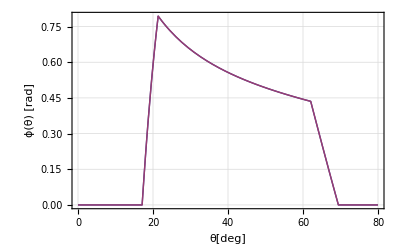

```mathematica
(* angle theta *)
ϕ1[θ_]:=ArcTan[X[θ],Y[θ]]2
ϕ2[θ_]:=2π-ArcTan[-X[θ],Y[θ]]2
Plot[{ϕ1[θ],ϕ2[θ]},{θ,0, 80},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Frame->True,FrameLabel->{Style["θ[deg]",12],Style["ϕ(θ) [rad]",12]},PlotRange->{0,All},ImageSize->400]
```

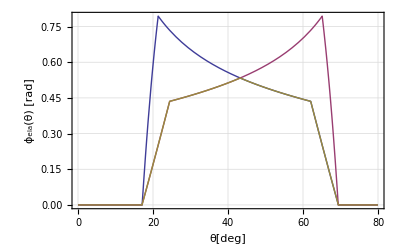

```mathematica
(* To Deal with elastics scattering correlation of L and R *)
ϕela[θ_]:=Min[ϕ1[θ],ϕ2[86.5-θ]];
Plot[{ϕ1[θ],ϕ2[86.5-θ],ϕela[θ ]},{θ,0,80},PlotRange->All,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Frame->True,FrameLabel->{Style["θ[deg]",12],Style["ϕ_ela(θ) [rad]",12]},ImageSize->400
]
```

```mathematica
Accp[θ1_,θ2_]:= NIntegrate[Sin[θ π/180]ϕela[θ],{θ,θ1,θ2}]
```

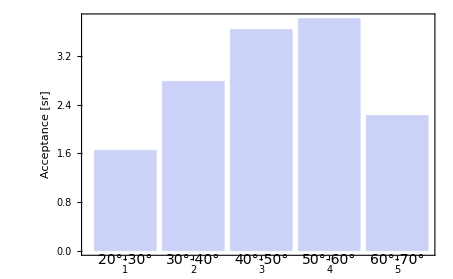

```mathematica
BarChart[Table[Accp[20+i, 30+i],{i,0,40,10}],
ChartLabels->{Style["20°-30°",14],Style["30°-40°",14],Style["40°-50°",14],Style["50°-60°",14],Style["60°-70°",14]},
Frame->True,FrameLabel->{"",Style["Acceptance [sr]",14]}]
```

```mathematica
NIntegrate[Dsc[θ 180/π] Sin[θ]ϕela[θ 180/π ],{θ,π/180 20,π/180 70}]
```

2.51459

### Yield Calculations

```mathematica
NB=1.275 10^5; (* pps *)
f=0.35;
NT=(1.14 (*g cm^-3 *))/(128.17 (* g mol^-1 *))(6.02214129 10^23(* mol^-1*))8 0.1 (*cm*) ;
ϵ=0.764; (* detector efficiency *)
α=0.77; (* DAQ life rate *)
dYLdT[P_,θ1_,θ2_]:=NB f NT ϵ α NIntegrate[Dsc[θ 180/π](1+Ay[θ 180/π]P) Sin[θ]ϕela[θ 180/π ],{θ,π/180 θ1,π/180 θ2}] 10^-27
dYRdT[P_,θ1_,θ2_]:=NB f NT ϵ α NIntegrate[Dsc[θ 180/π](1-Ay[θ 180/π]P)Sin[θ]ϕela[θ 180/π ],{θ,π/180 θ1,π/180 θ2}] 10^-27
dYdT[θ1_,θ2_]:=2NB f NT ϵ α NIntegrate[Dsc[θ 180/π] Sin[θ]ϕela[θ 180/π],{θ,π/180 θ1,π/180 θ2}] 10^-27
dΔYdT[P_,θ1_,θ2_]:=2NB f NT ϵ α NIntegrate[Dsc[θ 180/π]P Ay[θ 180/π]Sin[θ]ϕela[θ 180/π],{θ,π/180 θ1,π/180 θ2}] 10^-27
```

```mathematica
mp = 938.272 (*MeV *);
θLabtoθCM[θ_, T_]:=2ArcTan[Tan[θ π/180] √(1+T/(2 mp))] 180/π
θCMtoθLab[θ_,T_]:=ArcTan[Tan[θ/2 π/180] 1/(√(1+T/(2 mp)))] 180/π
```

```mathematica
Minimize[(2856-t 17.07418153216)^2+(2857-t 17.0508490803)^2,t]
```

{12.0353,{t→167.414}}

```mathematica
duration=1;
Pol=0.1313;
Timing[yield=Table[
{40+i,
dYLdT[Pol,θCMtoθLab[40+i,260],θCMtoθLab[60+i,260]]60 duration,
dYRdT[Pol,θCMtoθLab[40+i,260],θCMtoθLab[60+i,260]]60duration,
dYdT[θCMtoθLab[40+i,260],θCMtoθLab[60+i,260]]60duration,
dΔYdT[Pol,θCMtoθLab[40+i,260],θCMtoθLab[60+i,260]]60duration
},{i,0,80,20}];]
yield//TableForm
{Sum[yield[[i,2]],{i,1,5}],Sum[yield[[i,3]],{i,1,5}],Sum[yield[[i,4]],{i,1,5}],Sum[yield[[i,5]],{i,1,5}]}
```

{100.894,Null}

40 | 2.48056 | 2.27807 | 4.75863 | 0.202493
60 | 4.07125 | 3.87736 | 7.94861 | 0.193895
80 | 4.54946 | 4.54952 | 9.09897 | -0.0000609643
100 | 3.87749 | 4.07137 | 7.94886 | -0.193888
120 | 2.09285 | 2.2771 | 4.36996 | -0.184247

{17.0716,17.0534,34.125,0.0181921}

```mathematica
{dYdT[30,40], dYdT[θCMtoθLab[60 ,260],θCMtoθLab[80,260 ]]}60 time[[1]]/2
```

{808.525,764.587}

```mathematica
time={165, 114.3};
(* Theory total count *)
totcountUp=dYdT[15,70]60time[[1]]/2;
totcountDown=dYdT[15,70]60time[[2]]/2;
{totcountUp, √totcountUp}
{totcountDown, √totcountDown}
{totcountUp+totcountDown, √(totcountUp+totcountDown)}
```

{2825.04,53.1511}

{1956.98,44.2378}

{4782.02,69.1521}

```mathematica
(* yield *)
Manipulate[Plot[{NB NT ϵ f α Dsc[x](1+Ay[x]P)10^-27 Sin[x π/180]ϕela[x],NB NT ϵ f α Dsc[x](1-Ay[x]P)10^-27 Sin[x π/180]ϕela[x]},{x,15,70},PlotRange->{0,0.3},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Epilog->Text[Style["P="<>ToString[P],24],{53,1.5}],AxesLabel->{"θ","dY/dθdt"},ImageSize->600],{{P,0.2},0,1}]
```

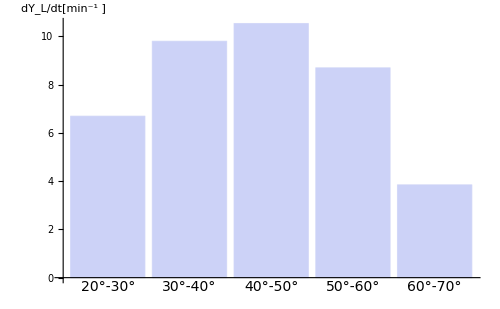

```mathematica
BarChart[Table[dYdT[20+i,30+i]60,{i,0,40,10}],ChartLabels->{Style["20°-30°",14],Style["30°-40°",14],Style["40°-50°",14],Style["50°-60°",14],Style["60°-70°",14]},AxesLabel->{"",Style["dY_L/dt[min^-1 ]",14]},ImageSize->500]
```

```mathematica
duration=1;
Pol=0.15;
Timing[yield=Table[
{20+i,
dYLdT[Pol,20+i,30+i]60 duration,
dYRdT[Pol,20+i,30+i]60duration,
dYdT[20+i,30+i]60duration,
dΔYdT[Pol,20+i,30+i]60duration
},{i,0,40,10}];]
yield//TableForm
{Sum[yield[[i,2]],{i,1,5}],Sum[yield[[i,3]],{i,1,5}],Sum[yield[[i,4]],{i,1,5}],Sum[yield[[i,5]],{i,1,5}]}
```

{100.47,Null}

20 | 3.00405 | 2.73756 | 5.74161 | 0.266488
30 | 4.3002 | 4.10519 | 8.40538 | 0.195009
40 | 4.49478 | 4.54151 | 9.03629 | -0.0467228
50 | 3.61014 | 3.85095 | 7.46108 | -0.240806
60 | 1.56764 | 1.73249 | 3.30013 | -0.164853

{16.9768,16.9677,33.9445,0.00911591}

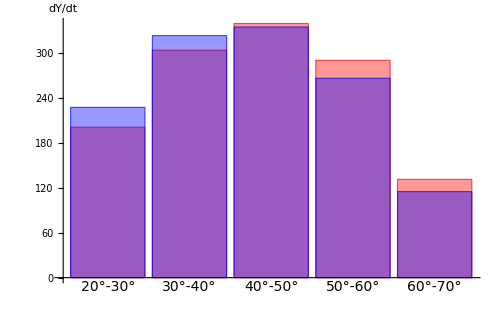

```mathematica
Show[
BarChart[Table[yield[[i,3]],{i,1,5}],ImageSize->500,ChartLabels->{Style["20°-30°",14],Style["30°-40°",14],Style["40°-50°",14],Style["50°-60°",14],Style["60°-70°",14]},ChartStyle->Directive[Opacity[0.4],Red],AxesLabel->{"",Style["dY/dt",14]}],
BarChart[Table[yield[[i,2]],{i,1,5}],ChartStyle->Directive[Opacity[0.4],Blue]]
]
```

### error propagation

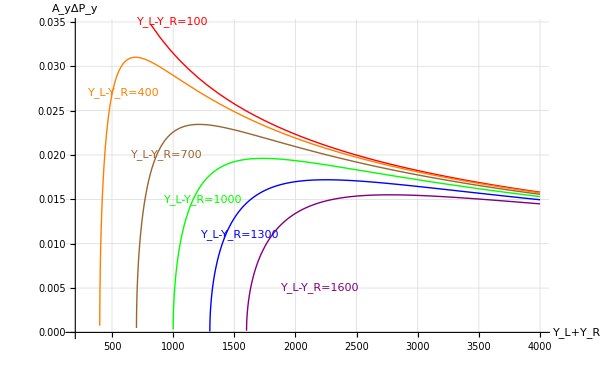

```mathematica
Plot[Evaluate[Table[√((4 (Y/2+Δ/2)(Y/2-Δ/2))/Y^3),{Δ,100,1600,300}]],{Y,200,4000},ImageSize->600,PlotStyle->{Red,Orange, Brown, Green,Blue, Purple, Black},AxesLabel->{"Y_L+Y_R","A_yΔP_y"},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Epilog->{{Red,Text["Y_L-Y_R=100",{1000,0.035}]},{Orange,Text["Y_L-Y_R=400",{600,0.027}]},{Brown,Text["Y_L-Y_R=700",{950,0.02}]},{Green,Text["Y_L-Y_R=1000",{1250,0.015}]},{Blue,Text["Y_L-Y_R=1300",{1550,0.011}]},{Purple,Text["Y_L-Y_R=1600",{2200,0.005}]}}]
```

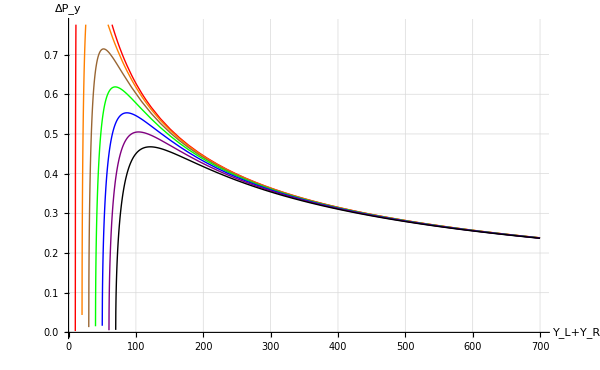

```mathematica
Plot[Evaluate[Table[1/Ay[35] √((4 (Y/2+Δ/2)(Y/2-Δ/2))/Y^3),{Δ,10,70,10}]],{Y,10,700},ImageSize->600,PlotStyle->{Red,Orange, Brown, Green,Blue, Purple, Black},AxesLabel->{"Y_L+Y_R","ΔP_y"},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]]
```

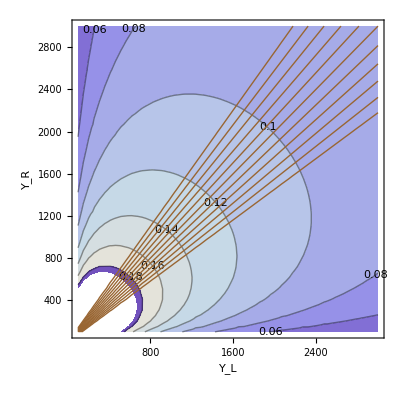

```mathematica
Show[
ContourPlot[1/Ay[35] √((4 A B)/(A+B)^3),{A,100,3000},{B,100,3000},ContourLabels->True,ImageSize->400,Frame->True,FrameLabel->{Style["Y_L",14],Style["Y_R",14]}],
ContourPlot[1/Ay[35](A-B)/(A+B),{A,100,3000},{B,100,3000},Contours->Table[-1+0.2 i,{i,0,10}],ContourShading->None,ContourStyle->Brown]
]
```

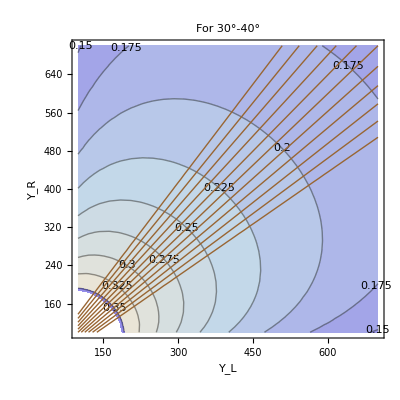

```mathematica
Show[
ContourPlot[1/Ay[35] √((4 A B)/(A+B)^3),{A,100,700},{B,100,700},ContourLabels->True,ImageSize->400,Frame->True,FrameLabel->{Style["Y_L",14],Style["Y_R",14]},PlotLabel->"For 30°-40°"],
ContourPlot[1/Ay[35](A-B)/(A+B),{A,100,700},{B,100,700},Contours->Table[-1+0.2 i,{i,0,10}],ContourShading->None,ContourStyle->Brown]
]
```

### Given Yield at range of angle, calculate the Polarization and Error

```mathematica
Py[θ1_,θ2_,YL_,YR_]:=1/Ay[(θ1+θ2)/2] (YL-YR)/(YL+YR)
DPy[θ1_,θ2_,YL_,YR_]:=2/Ay[(θ1+θ2)/2] √((YL YR)/(YL+YR)^3)
P[θ1_,θ2_,YL_,YR_]:={{"Ay",Ay[(θ1+θ2)/2]},{"Pol.",Py[θ1,θ2,YL,YR]},{"Abs Error",DPy[θ1,θ2,YL,YR]},{"% error",DPy[θ1,θ2,YL,YR]/Py[θ1,θ2,YL,YR] 100}}
Py2[θ1_,θ2_,YL1_,YR1_,YL2_,YR2_]:=1/Ay[(θ1+θ2)/2](√(YL1 YR2)-√(YL2 YR1))/(√(YL1 YR2)+√(YL2 YR1))
```

```mathematica
AngleCM={18.83,28.42,38.18,48.16,58.36,68.78}
```

{18.83,28.42,38.18,48.16,58.36,68.78}

```mathematica
Table[P[AngleCM[[i]],AngleCM[[i+1]],160,212],{i,1,5}]
```

{{{Ay,0.340246},{Pol.,-0.410835},{Abs Error,0.150887},{% error,-36.7268}},{{Ay,0.190109},{Pol.,-0.735289},{Abs Error,0.270048},{% error,-36.7268}},{{Ay,-0.000527127},{Pol.,265.183},{Abs Error,-97.3932},{% error,-36.7268}},{{Ay,-0.191062},{Pol.,0.731622},{Abs Error,-0.268701},{% error,-36.7268}},{{Ay,-0.340747},{Pol.,0.410231},{Abs Error,-0.150665},{% error,-36.7268}}}

```mathematica
Manipulate[
{test1={ML+BGL,MR+BGR}, 
test2={α (MR+BGL),α(ML+ BGR)},
test=√(test1 Reverse[test2]),
Py[20,30,test[[1]],test[[2]]]}//TableForm,{{ML,1000},0,1000},{{MR,800},0,1000}, {BGL,0, 1000},{BGR,0,1000},{α,1,5}]
```

## Data

```mathematica
Needs["ErrorBarPlots`"]
```

{{-0.747622,0.146105},{-0.519381,0.187013},{-1.0844,-0.708668},{-0.354603,-0.159208},{-1.0307,-0.182069}}

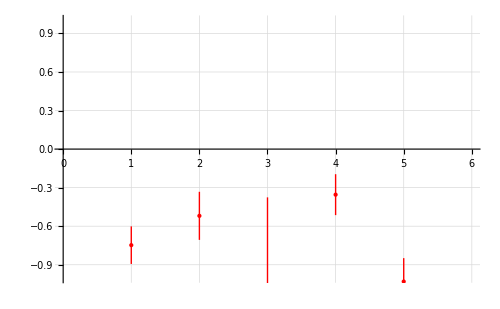

{{-0.284529,0.167778},{0.219865,0.21134},{0.0773815,-0.840179},{0.268192,-0.178512},{-0.782565,-0.217685}}

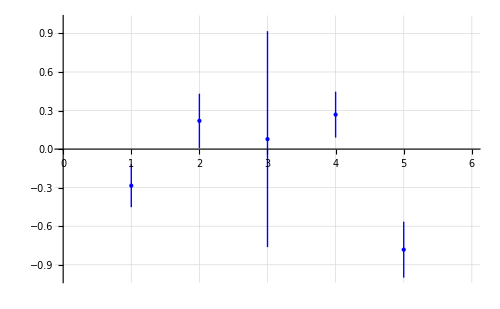

{{-0.238217,0.159937},{-0.369832,0.198889},{-0.581087,-0.771823},{-0.311426,-0.168596},{-0.138397,-0.216086}}

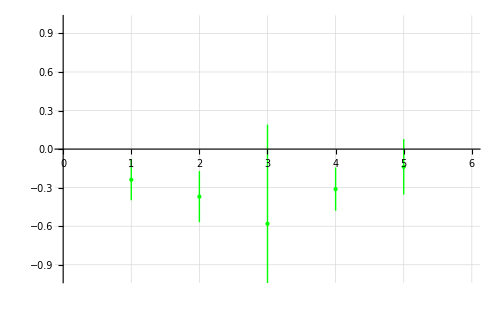

-0.273607

0.084878

```mathematica
mwdcL1={160,518,774,434,142};
mwdcR1={262,611,715,371,66};
mwdcL2={153,460,529,302,99};
mwdcR2={184,429,532,340,56};
mwdcL=√(mwdcL1 mwdcR2);
mwdcR=√(mwdcL2 mwdcR1);
Table[Transpose[P[10+i 10,20+i 10,mwdcL1[[i]],mwdcR1[[i]]]][[2]][[2;;3]],{i,1,5}]
ErrorListPlot[%,PlotRange->{{0,6},{-1,1}},PlotStyle->Red,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],ImageSize->500]
Table[Transpose[P[10+i 10,20+i 10,mwdcL2[[i]],mwdcR2[[i]]]][[2]][[2;;3]],{i,1,5}]
ErrorListPlot[%,PlotRange->{{0,6},{-1,1}},PlotStyle->Blue,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],ImageSize->500]
Pol=Table[Transpose[P[10+i 10,20+i 10,mwdcL[[i]],mwdcR[[i]]]][[2]][[2;;3]],{i,1,5}]
ErrorListPlot[%,PlotRange->{{0,6},{-1,1}},PlotStyle->Green,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],ImageSize->500]
WeigthedMean=Sum[Pol[[i,1]]/Pol[[i,2]]^2,{i,1,5}]/Sum[1/Pol[[i,2]]^2,{i,1,5}]
WeigthedSigm=√(Sum[(Pol[[i,1]]-WeigthedMean)^2/Pol[[i,2]]^2,{i,1,5}]/Sum[1/Pol[[i,2]]^2,{i,1,5}])
```

```mathematica
Total[mwdcL1]
Total[mwdcL2]
Total[mwdcL1]/Total[mwdcL2]//N
169.45/115.15
```

2129

1454

1.46424

1.47156

{{0.0966594,0.146064},{0.015882,0.1827},{-0.252067,-0.701926},{0.0653757,-0.150935},{0.243426,-0.200229}}

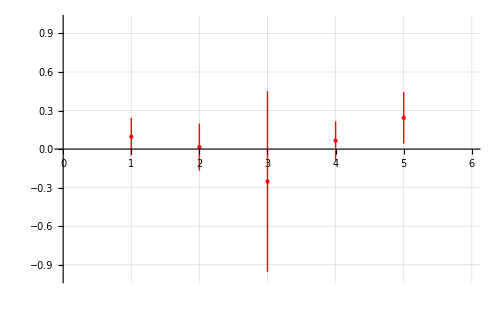

{{0.179599,0.17538},{-0.0380288,0.218984},{-0.134549,-0.858155},{0.0656672,-0.181805},{0.213703,-0.24482}}

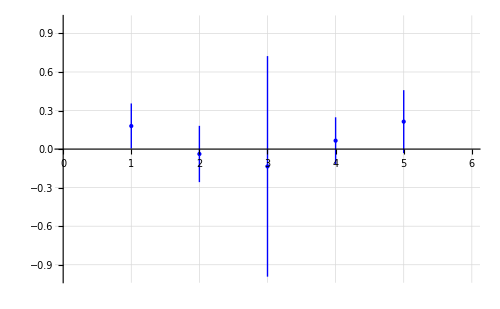

{{-0.0415529,0.160292},{0.0269555,0.200021},{-0.0587619,-0.776148},{-0.000145796,-0.165679},{0.0149598,-0.222501}}

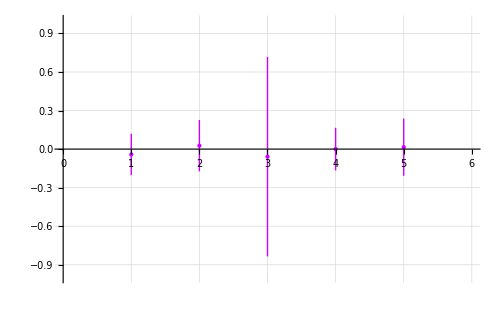

-0.00608969

0.0273009

```mathematica
mwdcL1={231,597,767,444,90};
mwdcR1={217,594,753,457,107};
mwdcL2={164,412,511,306,61};
mwdcR2={146,417,506,315,71};
mwdcL=√(mwdcL1 mwdcR2);
mwdcR=√(mwdcL2 mwdcR1);
Table[Transpose[P[10+i 10,20+i 10,mwdcL1[[i]],mwdcR1[[i]]]][[2]][[2;;3]],{i,1,5}]
ErrorListPlot[%,PlotRange->{{0,6},{-1,1}},PlotStyle->Red,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],ImageSize->500]
Table[Transpose[P[10+i 10,20+i 10,mwdcL2[[i]],mwdcR2[[i]]]][[2]][[2;;3]],{i,1,5}]
ErrorListPlot[%,PlotRange->{{0,6},{-1,1}},PlotStyle->Blue,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],ImageSize->500]
Pol=Table[Transpose[P[10+i 10,20+i 10,mwdcL[[i]],mwdcR[[i]]]][[2]][[2;;3]],{i,1,5}]
ErrorListPlot[%,PlotRange->{{0,6},{-1,1}},PlotStyle->Hue[0.8],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],ImageSize->500]
WeigthedMean=Sum[Pol[[i,1]]/Pol[[i,2]]^2,{i,1,5}]/Sum[1/Pol[[i,2]]^2,{i,1,5}]
WeigthedSigm=√(Sum[(Pol[[i,1]]-WeigthedMean)^2/Pol[[i,2]]^2,{i,1,5}]/Sum[1/Pol[[i,2]]^2,{i,1,5}])
```

```mathematica
Table[
Round[7{Cos[θ],Sin[θ]}+{0,11},0.01],{θ,0,2π,π/4}]//TableForm
```

7. | 11.
4.95 | 15.95
0. | 18.
-4.95 | 15.95
-7. | 11.
-4.95 | 6.05
0. | 4.
4.95 | 6.05
7. | 11.

```mathematica
mwdcL1={231,597,767,444,90};
mwdcR1={217,594,753,457,107};
mwdcL2={164,412,511,306,61};
mwdcR2={146,417,506,315,71};
```

```mathematica
a=(mwdcL1-mwdcL2)/(mwdcL1+mwdcL2)//N
b=(mwdcR1-mwdcR2)/(mwdcR1+mwdcR2)//N
```

{0.16962,0.18335,0.200313,0.184,0.192053}

{0.195592,0.175074,0.196187,0.183938,0.202247}

```mathematica
ay=Table[Ay[15+i 10],{i,1,5}]
```

{0.3233,0.1586,-0.03654,-0.2207,-0.3545}

```mathematica
P1=(2 a)/((1.8-0.2a)ay)
```

{0.594145,1.31121,-6.22979,-0.945679,-0.615078}

```mathematica
P2=(2 b)/((0.2 b-1.8)ay)
```

{-0.687141,-1.25086,6.09862,0.945353,0.648477}

```mathematica
(1.8 0.5 ay)/(2+0.2 0.5 ay)
```

{0.143171,0.0708085,-0.0164731,-0.100423,-0.162404}

```mathematica
(-(a+b)+2a b)/((a+b)+2 a b)
(-(a-b)-2a b)/(ay(a-b))
```

{-0.692502,-0.696185,-0.66913,-0.689234,-0.670818}

{4.80909,-55.2184,548.755,4937.32,-18.6754}